Coordenadas y gráficos

ListPlot y ListLinePlot se han venido usando para obtener los gráficos de listas de valores dados en forma consecutiva. Si se consideran listas compuestas de parejas de coordenadas, en vez de valores individuales, aquellas funciones podrán usarse para obtener los gráficos de puntos que estén en posiciones arbitrarias.

Represente gráficamente una lista de valores donde cada uno de ellos aparece después del anterior:

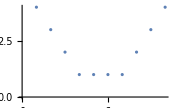

```mathematica
ListPlot[{4,3,2,1,1,1,1,2,3,4}]
```

Represente gráficamente una secuencia de puntos arbitrarios, especificados por sus coordenadas {x, y}:

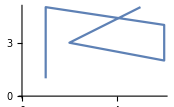

```mathematica
ListLinePlot[{{1,1},{1,5},{6,4},{6,2},{2,3},{5,5}}]
```

Aquí la posición de cada punto está especificada por sus coordenadas {x, y}. De acuerdo con el uso convencional en matemáticas, el valor x indica hasta qué distancia se encuentra el punto en la dirección horizontal, mientras que el valor y indica hasta qué distancia está en la dirección vertical.

Genere una secuencia de coordenadas {x, y} aleatorias:

```mathematica
Table[RandomInteger[20],10,2]
```

{{19,8},{11,20},{14,15},{5,8},{6,4},{16,14},{1,17},{10,7},{5,6},{17,2}}

Otra forma de obtener coordenadas aleatorias es:

```mathematica
RandomInteger[20,{10,2}]
```

{{2,2},{20,18},{16,2},{13,13},{6,15},{11,18},{10,20},{17,20},{8,14},{2,10}}

Represente gráficamente 100 puntos con coordenadas aleatorias:

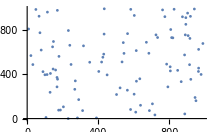

```mathematica
ListPlot[Table[RandomInteger[1000],100,2]]
```

Las coordenadas pueden usarse para construir gráficos. Anteriormente se vio cómo graficar un círculo. Para hacer gráficos de más de un círculo hay que indicar dónde queda cada uno, lo que se consigue dando las coordenadas de sus centros.

Sitúe varios círculos, dando las coordenadas de sus centros:

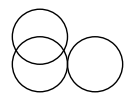

```mathematica
Graphics[{Circle[{1,1}],Circle[{1,2}],Circle[{3,1}]}]
```

Es más fácil distinguir cada uno de los círculos cuando se aplican estilos de color:

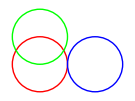

```mathematica
Graphics[{Style[Circle[{1,1}],Red],Style[Circle[{1,2}],Green],Style[Circle[{3,1}],Blue]}]
```

Presente gráficamente 100 círculos colocados al azar, donde las coordenadas de los centros estén entre 0 y 50:

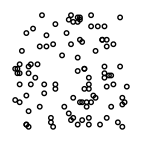

```mathematica
Graphics[Table[Circle[RandomInteger[50,2]],100]]
```

Un arreglo de círculos en 2D, acomodados de manera que apenas se toquen uno con otro:

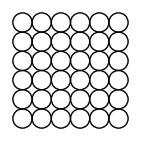

```mathematica
Graphics[Table[Circle[{x,y}],{x,0,10,2},{y,0,10,2}]]
```

Circle[{x,y}] quiere decir un círculo con centro en la posición {x,y}, y si no se dice otra cosa, ese círculo tiene radio 1. Pero puede hacerse un círculo de radio cualquiera usando Circle[{x,y},r].

Use radios diferentes para círculos diferentes:

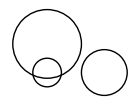

```mathematica
Graphics[{Circle[{1,1},0.5],Circle[{1,2},1.2],Circle[{3,1},0.8]}]
```

Cree 10 círculos concéntricos:

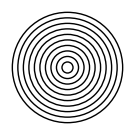

```mathematica
Graphics[Table[Circle[{0,0},r],{r,10}]]
```

Dibuje círculos cada vez más grandes cuyos centros se vayan corriendo progresivamente hacia la derecha:

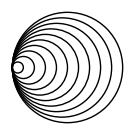

```mathematica
Graphics[Table[Circle[{x,0},x],{x,10}]]
```

Escoja al azar tanto las posiciones como los radios:

```mathematica
Graphics[Table[Circle[RandomInteger[50,2],RandomInteger[10]],100]]
```

-Graphics-

RegularPolygon funciona de manera muy parecida a Circle y Disk, salvo que, además de dar la posición del centro y el tamaño, hay que indicar de cuántos lados es el polígono.

Presente gráficamente un pentágono regular de tamaño 1 y un heptágono regular de tamaño 0.5:

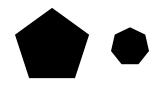

```mathematica
Graphics[{RegularPolygon[{1,1},1,5],RegularPolygon[{3,1},0.5,7]}]
```

Pueden mezclarse diferentes clases de objetos gráficos:

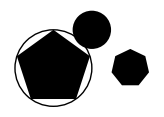

```mathematica
Graphics[{RegularPolygon[{1,1},1,5],Circle[{1,1},1],RegularPolygon[{3,1},.5,7],Disk[{2,2},.5]}]
```

Para producir gráficos arbitrarios es necesario utilizar las primitivas gráficas básicas Point, Line y Polygon. Point[{x,y}] representa un punto en la posición de coordenadas {x,y}. Para obtener varios puntos se puede dar una lista de Point[{x,y}]s, o bien una lista de coordenadas de posición dentro de un único Point.

Presentación gráfica de tres puntos en posiciones especificadas:

```mathematica
Graphics[{Point[{0,0}],Point[{2,0}],Point[{1,1.5}]}]
```

-Graphics-

La forma alternativa es reunir todas las coordenadas de posición en una sola lista:

```mathematica
Graphics[Point[{{0,0},{2,0},{1,1.5}}]]
```

-Graphics-

Dibuje una línea que una las posiciones:

```mathematica
Graphics[Line[{{0,0},{2,0},{1,1.5}}]]
```

-Graphics-

Haga un polígono cuyas esquinas estén en las posiciones que se indiquen:

```mathematica
Graphics[Polygon[{{0,0},{2,0},{1,1.5}}]]
```

-Graphics-

RegularPolygon construye un polígono en que todos los lados y los ángulos son iguales. Polygon hace un polígono cualquiera, aun si se quiere que se doble sobre sí mismo, por extraño que parezca.

Un polígono de 20 esquinas en posiciones aleatorias entre 0 y 100; este polígono se dobla sobre sí mismo:

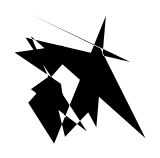

```mathematica
Graphics[Polygon[Table[RandomInteger[100],20,2]]]
```

Lo que se ha hecho hasta ahora puede generalizarse a 3D. En vez de dos coordenadas {x, y} ahora se usan tres: {x, y, z}. En Wolfram Language, la x aumenta hacia la derecha a través de la pantalla, la y se “mete dentro” de la pantalla, y la z aumenta de abajo hacia arriba.

Dos esferas apiladas, una encima de la otra:

```mathematica
Graphics3D[{Sphere[{0,0,0}],Sphere[{0,0,2}]}]
```

-Graphics3D-

Un arreglo en 3D de esferas (un radio común de 1/2 hace que apenas se toquen):

```mathematica
Graphics3D[Table[Sphere[{x,y,z},1/2],{x,5},{y,5},{z,5}]]
```

-Graphics3D-

Un arreglo de puntos en 3D:

```mathematica
Graphics3D[Table[Point[{x,y,z}],{x,10},{y,10},{z,10}]]
```

-Graphics3D-

50 esferas con posiciones aleatorias en 3D, donde cada coordenada varía entre 0 y 50:

```mathematica
Graphics3D[Table[Sphere[RandomInteger[10,3]],50]]
```

-Graphics3D-

Los objetos en 3D aparecen como sólidos, a menos que se indique otra cosa, de tal manera que no puede verse a través de ellos. Pero así como puede especificarse el color de algo, también puede especificarse su opacidad. Opacidad 1 significa completamente opaco, de modo que no puede verse nada a través del objeto; opacidad 0 quiere decir completamente transparente.

Especifique una opacidad de 0.5 para todas las esferas:

```mathematica
Graphics3D[Table[Style[Sphere[RandomInteger[10,3]],Opacity[0.5]],50]]
```

-Graphics3D-

El uso de Manipulate permite la manipulación de objetos gráficos en 2D o en 3D.

Manipule la posición y la opacidad de la segunda esfera:

```mathematica
Manipulate[Graphics3D[{Sphere[{0,0,0}],Style[Sphere[{x,0,0}],Opacity[o]]}],{x,1,3},{o,0.5,1}]
```

Vocabulario

Point[{x,y}] |   | un punto con coordenadas {x,y} 
Line[{{1,1},{2,4},{1,2}}] |   | una recta que conecta las coordenadas especificadas 
Circle[{x,y}] |   | un círculo con centro en {x,y} 
Circle[{x,y},r] |   | un círculo con centro en {x,y} y de radio r 
RegularPolygon[{x,y},s,n] |   | un polígono regular con centro {x,y}
y n lados, cada uno de longitud s 
Polygon[{{1,1},{2,4},{1,2}}] |   | un polígono con las esquinas especificadas 
Sphere[{x,y,z}] |   | una esfera con centro en {x,y,z} 
Sphere[{x,y,z},r] |   | una esfera con centro en {x,y,z} y de radio r
Opacity[level] |   | especifica un nivel de opacidad (0: transparente; 1: sólido)

"10 Exercises Available"
"with 6 extras" | "Get Started »"

Presente gráficamente 5 círculos concéntricos centrados en {0,0} con radios 1, 2, ... , 5. »

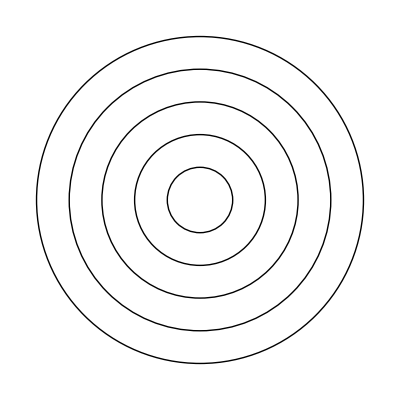
| Expected output: |  
  | -Graphics- |

Cree 10 círculos concéntricos con colores aleatorios. »

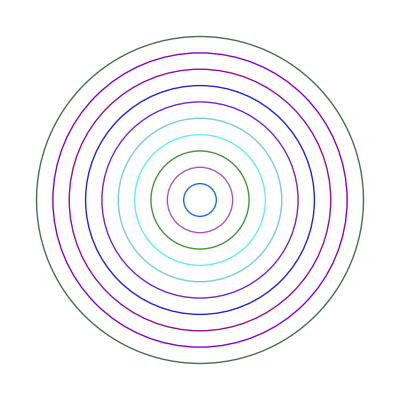
| Sample expected output: |  
  | -Graphics- |

Presente gráficamente una cuadrícula de 10×10 círculos de radio 1 en los puntos de coordenadas enteras {x,y}. »

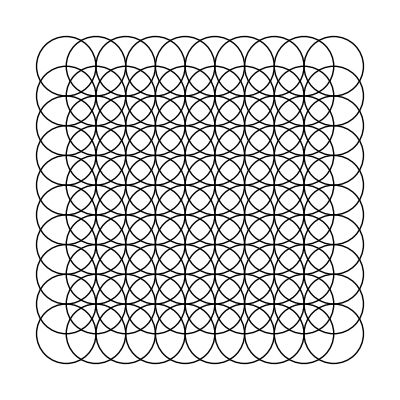
| Expected output: |  
  | -Graphics- |

Forme una cuadrícula de 10×10 puntos cuyas coordenadas sean enteras en las posiciones del 1 al 10. »

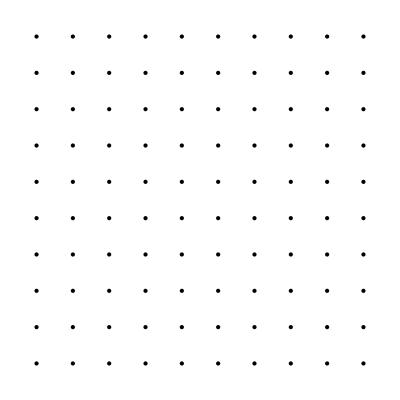
| Expected output: |  
  | -Graphics- |

Escriba un Manipulate con entre 1 y 20 círculos concéntricos. »

| Expected output: |  
  |  |

Coloque 50 esferas, de colores aleatorios, en coordenadas enteras aleatorias entre 0 y 10. »

| Sample expected output: |  
  | -Graphics3D- |

Haga un arreglo de 10×10×10 esferas con componentes RGB entre 0 y 1. Las esferas deben estar centradas en coordenadas enteras de manera que apenas se toquen una con otra. »

| Expected output: |  
  | -Graphics3D- |

Formule un Manipulate que contenga círculos de radio x, centrados en {t*x,0}, donde t varíe entre −2 y +2, y tal que x varíe entre 1 y 10. »

| Expected output: |  
  |  |

Forme un arreglo de 5×5 hexágonos regulares con lados de 1/2 y centrados en puntos enteros. »

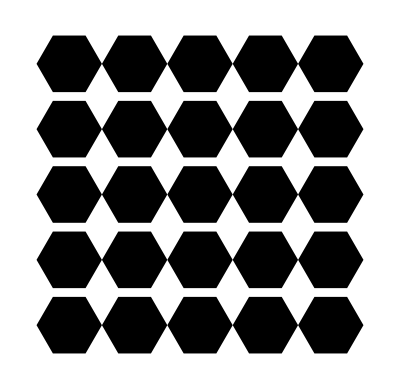
| Expected output: |  
  | -Graphics- |

Trace una línea en 3D que pase por 50 puntos con coordenadas enteras elegidas al azar entre 0 y 50. »

| Sample expected output: |  
  | -Graphics3D- |

Establezca un Manipulate para crear una cuadrícula regular de n×n puntos en posiciones enteras, donde n varíe de 5 a 20. »

| Expected output: |  
  |  |

Coloque 30 círculos de radio 1, con colores aleatorios, en coordenadas enteras al azar, entre 0 y 10. »

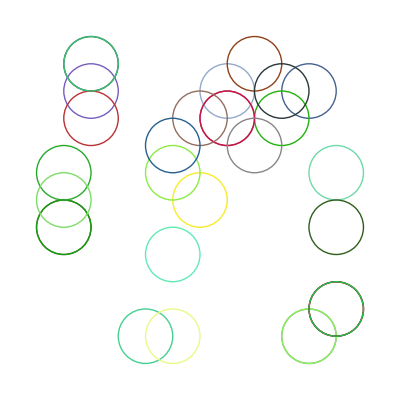
| Expected output: |  
  | -Graphics- |

Muestre 100 polÍgonos con tamaños de lado aleatorios entre 3 y 8, con opacidad de .5 y colores aleatorios y con coordenadas aleatorias enteras entre 0 y 100. »

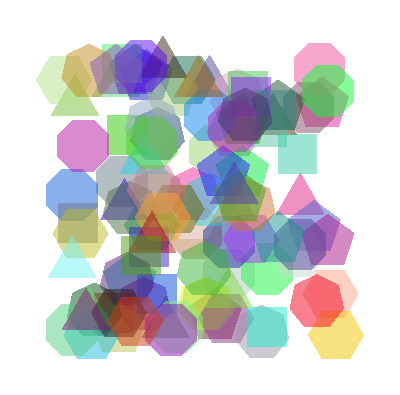
| Expected output: |  
  | -Graphics- |

Haga un arreglo de 10×10×10 puntos en 3D, donde cada punto tenga un color diferente. »

| Expected output: |  
  | -Graphics3D- |

Tome los dos primeros dígitos de los números del 10 al 100 y trazar una línea que los tenga como coordenadas. »

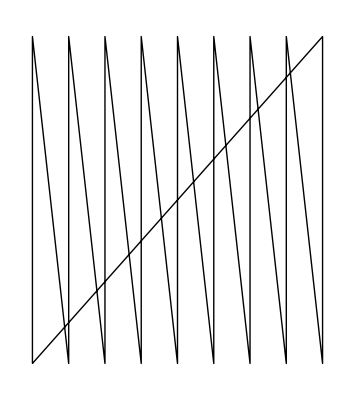
| Expected output: |  
  | -Graphics- |

Tome los 3 primeros dígitos de los números entre 100 y 1000 y dibujar una línea en 3D que los use como coordenadas. »

| Expected output: |  
  | -Graphics3D- |

Preguntas y respuestas

¿Qué es lo que determina la amplitud de las coordenadas que se muestran?

Por defecto, se selecciona automáticamente, pero se puede fijar explícitamente usando la opción PlotRange, como se explica en la Sección 20.

¿Cómo pueden colocarse ejes en los gráficos?

Usando la opción Axes→True (ver la Sección 20) .

¿Cómo puede cambiarse la apariencia de los bordes de un polígono o disco?

Usando EdgeForm dentro de Style.

¿Cuáles otras construcciones hay?

Hay bastantes. Algunos ejemplos son Text (para colocar texto dentro de un gráfico), Arrow (para colocar puntas de flecha en líneas, etc.), Inset (para poner gráficos dentro de otros gráficos) y FilledCurve.

¿Cómo se quita la caja alrededor de las gráficos 3D?

Usando la opción Boxed→False (ver la Sección 20) .

Notas técnicas

Los círculos aleatorios dibujados en esta sección tienen coordenadas enteras, pero se puede usar RandomReal para colocarlos en coordenadas arbitrarias.

En vez de usar Style, puede darse una lista de directivas para gráficos, tal como por ejemplo {Red,Disk[ ]}. Una directiva particular afecta a todos los objetos gráficos que aparezcan después dentro de dicha lista.

En gráficos 2D, los objetos se dibujan en el orden en que se escriben, así que los últimos que aparezcan pueden ocultar a los primeros.

Pueden aplicarse transformaciones geométricas a los objetos gráficos utilizando funciones como Translate, Scale y Rotate.

Los polígonos que se doblen sobre sí mismos (como para formar un corbatín) se muestran usando una regla de par-impar.

Los gráficos 3D pueden incluir Cuboid, Tetrahedron y poliedros especificados en PolyhedronData, así como formas definidas mediante mallas arbitrarias de puntos en el espacio 3D.

Paea explorar más

Guía para Graphics en Wolfram Language »